```mathematica
ρ:=16
m:=2.36
l:=Sqrt[20]
n:=ρ*l^2
d:=2
"causal events" n
"causal relations" n^2
A=CSDeSitterDGlobalSlabFull[l,d,n];
Subscript[C, 1]=CausalMatrix[A];
Subscript[T, 1]=DistanceMatrixC[A,All,"Timelike"];
T=Subscript[T, 1]*Subscript[C, 1];
V=(IdentityMatrix[n]+Subscript[C, 1]).(IdentityMatrix[n]+Subscript[C, 1]);
Subscript[T, 2]=Sqrt[2/ρ]*Sqrt[V];
K=1/2 Subscript[C, 1].Inverse[IdentityMatrix[n]+m^2/(2ρ)Subscript[C, 1]];
points:=Transpose[{Flatten[Subscript[T, 2]],Flatten[K]}];
```

320 causal events

102400 causal relations

$Aborted

Thread::tdlen: Objects of unequal length in {{1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, <<260>>, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0}, <<319>>} + <<1>> cannot be combined.

-Graphics-

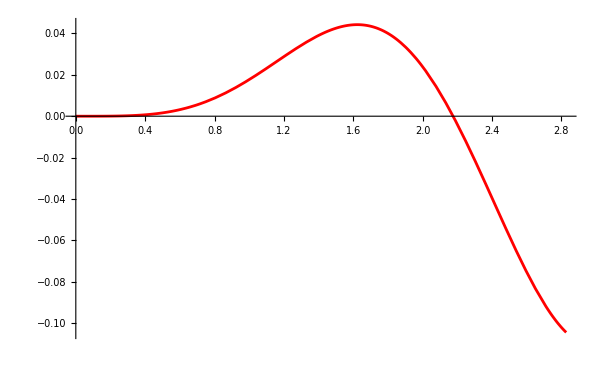

```mathematica
sample:=200000
(*ListPlot[RandomSample[points,sample],PlotStyle->PointSize[0.00001],ImageSize->600,AxesLabel->{"Matrix 1 entries","Matrix 2 entries"}]
Plot[1/2 BesselJ[0,m*x],{x,0,l}]
*)
Subscript[plot, 1]=ListPlot[RandomSample[points,sample],PlotStyle->PointSize[0.00001],ImageSize->600,AxesLabel->{"Proper time τ","Retarded Greens function"}];
Subscript[plot, 2]=Plot[1/2 BesselJ[0,m*τ]+τ^2/24 BesselJ[2,m*τ],{τ,0,l},PlotStyle->Red];
Show[Subscript[plot, 1],Subscript[plot, 2]]
Plot[τ^2/24 BesselJ[2,m*τ],{τ,0,l},PlotStyle->Red]
```